# Dicke Linsen

```mathematica
Needs["ErrorBarPlots`"]
```

-Graphics-

-Graphics-

## Funktionen

### Fehlerfunktion(Größtfehler) ∑(|df/dx_i|Δx_i)

```mathematica
GError[a_,b_,c_]:= (Total[Map[Abs,MapThread[D,{Table[a,{i,1,Length[b]}],b}]]*c]);
```

### Gauss

```mathematica
Gauss[a0_]:= Module[{a=a0},{Mean[a],StandardDeviation[a]/(√Length[a])}];
```

### Basics

```mathematica
fAdd[va_,dva_,vb_,dvb_]:=Module[{f,fe,a,b,da,db},
f=a+b;
fe=GError[f,{a,b},{da,db}];
{f,fe}/.{a->va,b->vb,da->dva,db->dvb}]
```

```mathematica
fSub[va_,dva_,vb_,dvb_]:=Module[{f,fe,a,b,da,db},
f=a-b;
fe=GError[f,{a,b},{da,db}];
{f,fe}/.{a->va,b->vb,da->dva,db->dvb}]
```

```mathematica
fDiv[va_,dva_,vb_,dvb_]:=Module[{f,fe,a,b,da,db},
f=a/b;
fe=GError[f,{a,b},{da,db}];
{f,fe}/.{a->va,b->vb,da->dva,db->dvb}]
```

```mathematica
fDiv1[va_,dva_]:=Module[{f,fe,a,da},
f=1/a;
fe=GError[f,{a},{da}];
{f,fe}/.{a->va,da->dva}]
```

```mathematica
fMult[va_,dva_,vb_,dvb_]:=Module[{f,fe,a,b,da,db},
f=a*b;
fe=GError[f,{a,b},{da,db}];
{f,fe}/.{a->va,b->vb,da->dva,db->dvb}]
```

## 1.) Vermessung des Abstandes Kathethometer{Gegenstand u, sowie Abmessen des Gegenstandes (cm-Maßstab, mindestens 10 Messungen)

ut/du/u: Abstand Kathetometer zum Gegenstand
gt/dg/g: Größe des Gegenstandes

```mathematica
ut = {{5.9, 5.9, 5.9, 5.9, 6.0}}10^-2;
du= 10^-3;
u = 3*10^-2;
u = Table[{fSub[ut[[1,x]],du,u,du]},{x,1,Length[ut[[1]]]}] //N
```

{{{0.029,0.002}},{{0.029,0.002}},{{0.029,0.002}},{{0.029,0.002}},{{0.03,0.002}}}

```mathematica
ug = Gauss[Table[{u[[x,1,1]]},{x,1,Length[u]}]]//N
```

{{0.0292},{0.0002}}

```mathematica
gt1 = {{4.366, 4.760, 4.774, 4.770, 4.750}}*10^-2;
```

```mathematica
gt2 = {{5.362, 5.762, 5.782, 5.772, 5.720}} 10^-2;
dg=10^-5;
```

```mathematica
gt = Table[{fSub[gt2[[1,x]],dg,gt1[[1,x]],dg]},{x,1,Length[gt1[[1]]]}] //N
```

{{{0.00996,0.00002}},{{0.01002,0.00002}},{{0.01008,0.00002}},{{0.01002,0.00002}},{{0.0097,0.00002}}}

```mathematica
g = Gauss[Table[{gt[[x,1,1]]},{x,1,Length[gt]}]]//N
```

{{0.009956},{0.0000667533}}

## 2.) Bestimmung der Abhängigkeit des Abbildungsmaßstabes - von der Bildweite a für die erste Lage des Linsensystems (mindestens 10 verschiedene AbstÄande a!).

yb/dyb : Größe der Bildes
a/da : Bildabstand
β ca zwischen 2 und 6

```mathematica
y1 = {{4.010, 3.636, 4.038, 4.032, 4.016, 4.038, 3.910, 3.968, 4.046, 4.039}} 10^-2;
y2 = {{4.930, 5.210, 4.792, 4.670, 4.578, 4.524, 5.072, 5.012, 4.612, 4.746}}10^-2;
dyb = 10^-5;
a1 ={{50.0, 40.0, 55.0, 60.0, 65.0, 70.0, 45.0, 47.0, 63.0, 57.0}}*10^-2;
a2 = {{122.2, 127.0, 123.4, 125.9, 129.2, 132.6, 122.5, 122.2, 127.7, 124.2}}*10^-2;
da = 10^-3;
```

```mathematica
ag = Table[{fSub[a2[[1,x]],da,a1[[1,x]],da]},{x,1,Length[a1[[1]]]}]//N
```

{{{0.722,0.002}},{{0.87,0.002}},{{0.684,0.002}},{{0.659,0.002}},{{0.642,0.002}},{{0.626,0.002}},{{0.775,0.002}},{{0.752,0.002}},{{0.647,0.002}},{{0.672,0.002}}}

```mathematica
ybt = Table[{fSub[y2[[1,x]],dyb,y1[[1,x]],dyb]},{x,1,Length[y2[[1]]]}]//N
```

{{{0.0092,0.00002}},{{0.01574,0.00002}},{{0.00754,0.00002}},{{0.00638,0.00002}},{{0.00562,0.00002}},{{0.00486,0.00002}},{{0.01162,0.00002}},{{0.01044,0.00002}},{{0.00566,0.00002}},{{0.00707,0.00002}}}

```mathematica
at = Table[{fSub[ag[[x,1,1]],ag[[x,1,2]],ug[[1]],u[[1,1,2]]]},{x,1,Length[ag]}]
```

{{{{0.6928},0.004}},{{{0.8408},0.004}},{{{0.6548},0.004}},{{{0.6298},0.004}},{{{0.6128},0.004}},{{{0.5968},0.004}},{{{0.7458},0.004}},{{{0.7228},0.004}},{{{0.6178},0.004}},{{{0.6428},0.004}}}

```mathematica
βt= Table[{fDiv[ybt[[x,1,1]],ybt[[x,1,2]],g[[1,1]],g[[2,1]]]},{x,1,Length[ybt]}];TableForm[βt]
```

0.924066
0.00820454
1.58096
0.0126089
0.757332
0.00708662
0.64082
0.00630542
0.564484
0.00579361
0.488148
0.00528179
1.16714
0.00983428
1.04861
0.00903962
0.568501
0.00582054
0.710125
0.0067701

## 3.)

```mathematica
p1=Table[{{at[[x,1,1,1]],βt[[x,1,1]]},ErrorBar[at[[x,1,2]],βt[[x,1,2]]]},{x,1,Length[at]}]//N
```

{{{0.6928,0.924066},ErrorBar[0.004,0.00820454]},{{0.8408,1.58096},ErrorBar[0.004,0.0126089]},{{0.6548,0.757332},ErrorBar[0.004,0.00708662]},{{0.6298,0.64082},ErrorBar[0.004,0.00630542]},{{0.6128,0.564484},ErrorBar[0.004,0.00579361]},{{0.5968,0.488148},ErrorBar[0.004,0.00528179]},{{0.7458,1.16714},ErrorBar[0.004,0.00983428]},{{0.7228,1.04861},ErrorBar[0.004,0.00903962]},{{0.6178,0.568501},ErrorBar[0.004,0.00582054]},{{0.6428,0.710125},ErrorBar[0.004,0.0067701]}}

```mathematica
pp = Table[{at[[x,1,1,1]],βt[[x,1,1]]},{x,1,Length[at]}]//N
```

{{0.6928,0.924066},{0.8408,1.58096},{0.6548,0.757332},{0.6298,0.64082},{0.6128,0.564484},{0.5968,0.488148},{0.7458,1.16714},{0.7228,1.04861},{0.6178,0.568501},{0.6428,0.710125}}

```mathematica
pf1=LinearModelFit[pp,x,x]
```

FittedModel[-2.18505+4.48434 x]

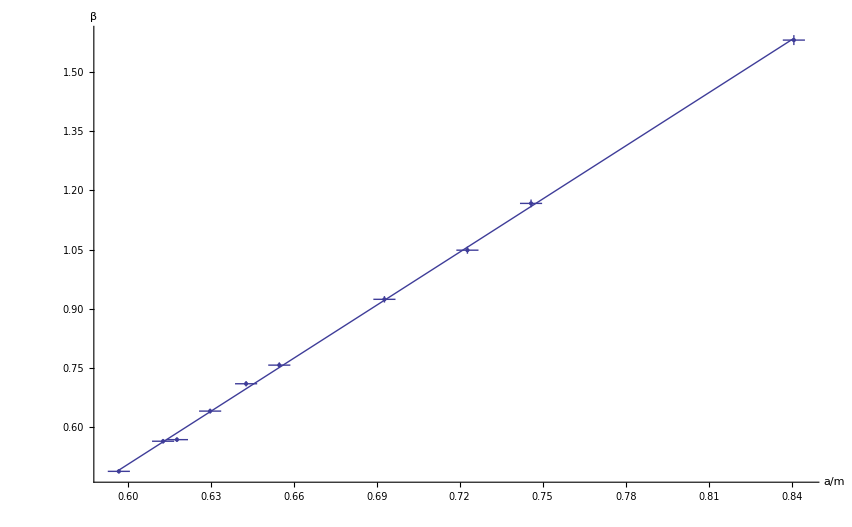

```mathematica
Show[
 ErrorListPlot[p1],
Plot[pf1[x],{x,Min[Table[{at[[x,1,1]]},{x,1,Length[at]}]],Max[Table[{at[[x,1,1]]},{x,1,Length[at]}]]}],AxesLabel->{"a/m","β"}]
```

```mathematica
pf1["ParameterTable"]
para1 = pf1["ParameterTableEntries"];
(*f1 = 1/para1[[2,1]]*)

(*c1 = para1[[1,1]]*-f1*)
```

| Estimate | Standard Error | t Statistic | P-Value
1 | -2.18505 | 0.0266685 | -81.9337 | 5.49105×10^-13
x | 4.48434 | 0.0392458 | 114.263 | 3.84607×10^-14

```mathematica
f1 = fDiv1[para1[[2,1]],para1[[2,2]]]
```

{0.222998,0.00195162}

```mathematica
c1 = fMult[para1[[1,1]],para1[[1,2]],-1*f1[[1]],f1[[2]]]
```

{0.487262,0.0102114}

```mathematica
h1 = fSub[c1[[1]],c1[[2]],f1[[1]],f1[[2]]]
```

{0.264264,0.0121631}

## 4.)

yb2/dyb2 : Größe der Bildes, bei umgedrehter Lage des Linsensystems
a2/da2 : Bildabstand, bei umgedrehter Lage des Linsensystems
β2 ca zwischen 2 und 6

```mathematica
y12 = {{2.882, 2.956, 3.018, 3.066, 3.128, 3.250, 3.324, 3.354, 3.374, 3.422}} 10^-2;
y22 = {{4.1, 4.112, 4.118, 4.118, 4.128, 4.134, 4.142, 4.140, 4.140, 4.150}}10^-2;
dyb2 = 10^-5;
a12 ={{700, 710, 720, 730, 740, 770, 790, 800, 810, 820}}*10^-3;
a22 = {{1227, 1222, 1220, 1220, 1218, 1221, 1226, 1230, 1234, 1239}}*10^-3;
da2= 10^-3;
```

```mathematica
ag2 = Table[{fSub[a22[[1,x]],da2,a12[[1,x]],da2]},{x,1,Length[a12[[1]]]}]//N
```

{{{0.527,0.002}},{{0.512,0.002}},{{0.5,0.002}},{{0.49,0.002}},{{0.478,0.002}},{{0.451,0.002}},{{0.436,0.002}},{{0.43,0.002}},{{0.424,0.002}},{{0.419,0.002}}}

```mathematica
ybt2 = Table[{fSub[y22[[1,x]],dyb2,y12[[1,x]],dyb2]},{x,1,Length[y22[[1]]]}]//N
```

{{{0.01218,0.00002}},{{0.01156,0.00002}},{{0.011,0.00002}},{{0.01052,0.00002}},{{0.01,0.00002}},{{0.00884,0.00002}},{{0.00818,0.00002}},{{0.00786,0.00002}},{{0.00766,0.00002}},{{0.00728,0.00002}}}

```mathematica
at2 = Table[{fSub[ag2[[x,1,1]],ag2[[x,1,2]],ug[[1]],u[[1,1,2]]]},{x,1,Length[ag2]}]
```

{{{{0.4978},0.004}},{{{0.4828},0.004}},{{{0.4708},0.004}},{{{0.4608},0.004}},{{{0.4488},0.004}},{{{0.4218},0.004}},{{{0.4068},0.004}},{{{0.4008},0.004}},{{{0.3948},0.004}},{{{0.3898},0.004}}}

```mathematica
βt2= Table[{fDiv[ybt2[[x,1,1]],ybt2[[x,1,2]],g[[1,1]],g[[2,1]]]},{x,1,Length[ybt2]}];TableForm[βt2]
```

1.22338
0.0102114
1.16111
0.00979388
1.10486
0.00941675
1.05665
0.00909349
1.00442
0.0087433
0.887907
0.0079621
0.821615
0.00751763
0.789474
0.00730212
0.769385
0.00716744
0.731217
0.00691153

## 5.)

```mathematica
p2=Table[{{at2[[x,1,1,1]],βt2[[x,1,1]]},ErrorBar[at2[[x,1,2]],βt2[[x,1,2]]]},{x,1,Length[at2]}]//N
```

{{{0.4978,1.22338},ErrorBar[0.004,0.0102114]},{{0.4828,1.16111},ErrorBar[0.004,0.00979388]},{{0.4708,1.10486},ErrorBar[0.004,0.00941675]},{{0.4608,1.05665},ErrorBar[0.004,0.00909349]},{{0.4488,1.00442},ErrorBar[0.004,0.0087433]},{{0.4218,0.887907},ErrorBar[0.004,0.0079621]},{{0.4068,0.821615},ErrorBar[0.004,0.00751763]},{{0.4008,0.789474},ErrorBar[0.004,0.00730212]},{{0.3948,0.769385},ErrorBar[0.004,0.00716744]},{{0.3898,0.731217},ErrorBar[0.004,0.00691153]}}

```mathematica
pp2 = Table[{at2[[x,1,1,1]],βt2[[x,1,1]]},{x,1,Length[at2]}]//N
```

{{0.4978,1.22338},{0.4828,1.16111},{0.4708,1.10486},{0.4608,1.05665},{0.4488,1.00442},{0.4218,0.887907},{0.4068,0.821615},{0.4008,0.789474},{0.3948,0.769385},{0.3898,0.731217}}

```mathematica
pf2=LinearModelFit[pp2,x,x]
```

FittedModel[-1.00758+4.48591 x]

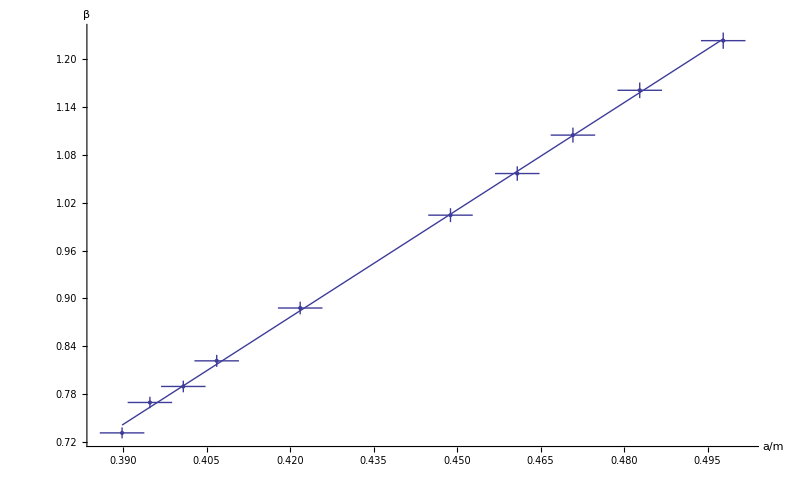

```mathematica
Show[
 ErrorListPlot[p2],
Plot[pf2[x],{x,Min[Table[{at2[[x,1,1]]},{x,1,Length[at2]}]],Max[Table[{at2[[x,1,1]]},{x,1,Length[at2]}]]}],AxesLabel->{"a/m","β"}]
```

```mathematica
pf2["ParameterTable"]
para2 = pf2["ParameterTableEntries"];
```

| Estimate | Standard Error | t Statistic | P-Value
1 | -1.00758 | 0.0177822 | -56.6626 | 1.04462×10^-11
x | 4.48591 | 0.0404961 | 110.774 | 4.9283×10^-14

```mathematica
f2 = fDiv1[para2[[2,1]],para2[[2,2]]]
```

{0.22292,0.00201239}

```mathematica
c2 = fMult[para2[[1,1]],para2[[1,2]],-1*f2[[1]],f2[[2]]]
```

{0.224611,0.00599165}

```mathematica
h2 = fSub[c2[[1]],c2[[2]],f2[[1]],f2[[2]]]
```

{0.00169051,0.00800404}